```mathematica
tp=0.4;   c=6.25;
f1[x_,d_]=Sqrt[d^2+(c*x)^2+tp^2/2+tp*(tp^2/4+(c*x)^2)^(1/2)];
f2[x_,d_]=-Sqrt[d^2+(c*x)^2+tp^2/2+tp*(tp^2/4+(c*x)^2)^(1/2)];
f3[x_,d_]=-Sqrt[d^2+(c*x)^2+tp^2/2-tp*(tp^2/4+(c*x)^2)^(1/2)];
f4[x_,d_]=Sqrt[d^2+(c*x)^2+tp^2/2-tp*(tp^2/4+(c*x)^2)^(1/2)];
v1[x_,d_]=tp/2+Sqrt[(c*x)^2+(tp/2+d1)^2];
v2[x_,a_]=tp/2-Sqrt[(c*x)^2+(tp/2+a)^2];
v3[x_,a_]=-tp/2+Sqrt[(c*x)^2+(tp/2-a)^2];
v4[x_,d_]=-tp/2-Sqrt[(c*x)^2+(tp/2-d)^2];

Manipulate[Labeled[diap,Plot[{f3[x-r,a+df],f4[x,a-rf]},{x,-0.15,diap[[1]]},PlotRange->{-0.7,diap[[2]]},PlotStyle->{Color},Frame->tR]],{{a,-0.15,"Gate voltage"},-0.15,0.15},{{Color,Red,"Color of grafic"},Red},{tR,{True,False}},{r,{0,0.015,0.02,0.033},ControlType->PopupMenu},{df,{0.1,0.2,0}},{rf,{-0.5->"value 1",0.5->"value 2",0->"value zero"}},{diap,{-0.2,-0.9},{0.4,1}}]
```

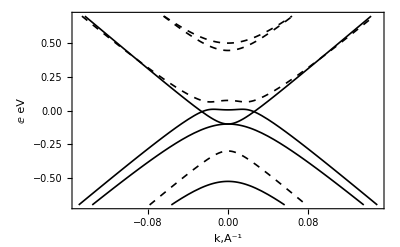

```mathematica
Plot[{f1[x],f2[x],f3[x],f4[x],v1[x],v2[x],v3[x],v4[x]},{x,-0.15,0.15},AxesLabel->{"k,A^-1",E eV},PlotRange->{-0.7,0.7},{PlotStyle->{{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black}},{Thickness[0.003],Black},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed}}},Frame->True]
```

```mathematica
Export["f1.pdf",Plot[{f1[x],f2[x],f3[x],f4[x],v1[x],v2[x],v3[x],v4[x]},{x,-0.15,0.15},AxesLabel->{"k,A^-1",E eV},PlotRange->{-0.7,0.7},{PlotStyle->{{{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black},{Thickness[0.003],Black}},{Thickness[0.003],Black},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed},{Thickness[0.003],Black,Dashed}}},Frame->True]]
```

f1.pdf

```mathematica
"f1.pdf"
Framed[Manipulate[Plot[{v2[x,a],v3[x,a]},{x,-0.15,0.15},PlotRange->{-0.7,0.7}],{a,-0.15,0.15},Alignment->{Right,Right},ContentSize->{400,400}],RoundingRadius->20]
```

f1.pdf